```mathematica
SetDirectory[NotebookDirectory[]];
```

### Look at how the parameters changed

```mathematica
data=Import["paramsnoip.50.1000.0005.dat"];
data=Transpose[data][[3;;39]];
Manipulate[ListPlot[data[[n]],PlotRange->All,PlotLegends->{StringJoin["Mean=",ToString[Mean[data[[n]][[a;;50]]]]]},GridLines->{{a},{}}],{n,1,37,1},{a,1,50,1}]
```

```mathematica
data=Import["paramsip.50.1000.0005.dat"];
data=Transpose[data][[3;;39]];
Manipulate[ListPlot[data[[n]],PlotRange->All,PlotLegends->{StringJoin["Mean=",ToString[Mean[data[[n]][[a;;50]]]]]},GridLines->{{a},{}}],{n,1,37,1},{a,1,50,1}]
```

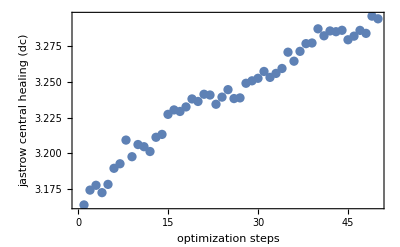

```mathematica
p1=ListPlot[data[[1]],Frame->{{True,False},{True,False}},
FrameStyle->15,FrameLabel->{"optimization steps","jastrow central healing (dc)"}]
(*Export["~/Desktop/plot.pdf",p1]*)
```

```mathematica
data=Import["paramsnoip.200.1000.0005.dat"];
data=Transpose[data][[3;;39]];
Manipulate[ListPlot[data[[n]],PlotRange->All,PlotLegends->{StringJoin["Mean=",ToString[Mean[data[[n]][[a;;200]]]]]},GridLines->{{a},{}}],{n,1,37,1},{a,1,200,1}]
```

9.941911909180412468+0.0192166553363155012 x-0.000038625161029047995 x^2

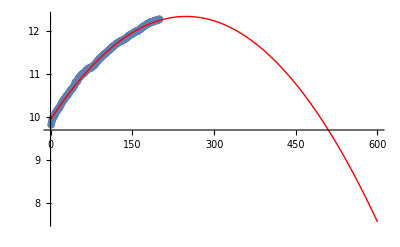

{12.332062736234743}

```mathematica
myfit=Fit[data[[2]],{1,x,x^2},x]
p1=ListPlot[data[[2]]];
p2=Plot[myfit,{x,0,600},PlotStyle->{Thick,Red}];
Show[p1,p2,PlotRange->All]

sol=Solve[D[myfit,x]==0,x];
myfit/.sol
```

```mathematica
data=Import["paramsip.200.1000.0005.dat"];
data=Transpose[data][[3;;39]];
Manipulate[ListPlot[data[[n]],PlotRange->All,PlotLegends->{StringJoin["Mean=",ToString[Mean[data[[n]][[a;;34]]]]]},GridLines->{{a},{}}],{n,1,37,1},{a,1,34,1}]
```

```mathematica
data1=Import["paramsnoip.200.1000.0005.dat"];
data2=Import["paramsnoip.200.1000.0005.2.dat"];
data1=Transpose[data1][[3;;39]];
data2=Transpose[data2][[3;;39]];
Do[
data[[i]]=Flatten[Append[data1[[i]],data2[[i]]]],
{i,37}
]
Manipulate[ListPlot[data[[n]],PlotRange->All,PlotLegends->{StringJoin["Mean=",ToString[Mean[data[[n]][[a;;400]]]]]},GridLines->{{a},{}}],{n,1,37,1},{a,1,400,1}]
```